## Calculating the cloverleaf configuration with MOT coils using radia:

```mathematica
Clear["Global`*"]
```

### First, load the Radia package :

```mathematica
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

### Next, let’s define the geometry, first for the anti-bias and curvature coils:

#### Geometry definitions:

```mathematica
(* Let's start by defining the radial thickness of a winding: *)
rth  =1/2*25.4; (* Bitter coils used in Chin's group were 19.25 mm (3/4 in) *)
rspac = 0.05*25.4; (* Spacing between concentric coils *)

(* Let's define the inner radius *)
rcurv =1.25*25.4/2+rth/2; (* 1 in beam perhaps? 1.25" fits a 1" beam comfortably *)

curvturns1 = 6;  (* including brass spacer below *)
curvturns2 = 5;
biasturns1 = 6;
biasturns2 = 6;

zthcop=1;  (* thickness of the copper windings *)
zthbrass =.205*25.4;(* thickness of the brass bottom piece *)
zsep = 0.254; (* separation between windings *)
biasbrassfrac=1;
zsepbias = 2*zsep; (* increase height of bias cooling channels *)
cbdiff=0.019*25.4;(* increase recess of curvature coil *)
Lin=3*25.4;(* length of input current leads *)
Xin=0.15*25.4;(* width of input current leads *)

(* If using the glass cell, it is about 1 1/8 in thick.  Leave 1/8 of an inch on either side  *)
zoff= 25.4*(1+4/8)/2; (* Z position of the first curvature/anti-bias coils *)

(* Now calculate the offsets for the two coils *)
zoffcurv1 = zoff+(Max[curvturns1*(zthcop+zsep),curvturns2*(zthcop+zsep)(*,biasturns1*(zthcop+zsepbias),biasturns2*(zthcop+zsepbias)*)]-curvturns1*(zthcop+zsep))+cbdiff;
zoffbias1 = zoff+(Max[(*curvturns1*(zthcop+zsep),curvturns2*(zthcop+zsep),*)biasturns1*(zthcop+zsepbias),biasturns2*(zthcop+zsepbias)]-biasturns1*(zthcop+zsepbias));
zoffcurv2 = zoff+(Max[curvturns1*(zthcop+zsep),curvturns2*(zthcop+zsep)(*,biasturns1*(zthcop+zsepbias),biasturns2*(zthcop+zsepbias)*)]-curvturns2*(zthcop+zsep))+cbdiff;
zoffbias2 = zoff+(Max[(*curvturns1*(zthcop+zsep),curvturns2*(zthcop+zsep),*)biasturns1*(zthcop+zsepbias),biasturns2*(zthcop+zsepbias)]-biasturns2*(zthcop+zsepbias));

(* Let's now define the radius of the bias coil to make it a Hemholtz coil *)
(* rbias = 2*zoff+(zthcop+zsep)*(biasturns-1) + (zthbrass+zsep); *)
(* Alternatively, we can just define it *)
(*rbias =(2+28/64)*25.4;*)
rbias=2.43*25.4;

(* Now define the currents: *)
Icurv=1;
Ibias = -1;

(* And finally, define the colors for a drawing: *)
colorcurv = {1,0,0};
colorbias = {0,0,1};
colorbiasBRASS = {0.33,0.33,1};
colorcurvBRASS= {1,0.33,0.33};
colorbiaslead = {0.5,0.5,1};
colorcurvlead = {1,0.5,0.5};
```

#### Actually make the coils:

```mathematica
n=5;

TransStackCoilsPos =radTrfTrsl[{0,0,zthcop+zsep}]; 
TransStackCoilsNeg =radTrfTrsl[{0,0,-zthcop-zsep}]; 
TransStackBiasCoilsPos =radTrfTrsl[{0,0,zthcop+zsepbias}]; 
TransStackBiasCoilsNeg =radTrfTrsl[{0,0,-zthcop-zsepbias}];

AntiBiasCoilTop1BRASS = radObjRaceTrk[{0.,0.,zoffbias1+zthbrass/2+zthbrass (1-biasbrassfrac)/2},{rbias-rth/2,rbias+rth/2},{0.,0.},biasbrassfrac zthbrass,n,Ibias/(biasbrassfrac zthbrass)/rth];
AntiBiasCoilTop1 = radObjRaceTrk[{0.,0.,zoffbias1+zthbrass+zsepbias+zthcop/2},{rbias-rth/2,rbias+rth/2},{0.,0.},zthcop,n,Ibias/zthcop/rth];
AntiBiasCoilTop2BRASS = radObjRaceTrk[{0.,0.,zoffbias2+zthbrass/2+zthbrass (1-biasbrassfrac)/2},{rbias+rth+rspac-rth/2,rbias+rth+rspac+rth/2},{0.,0.},biasbrassfrac zthbrass,n,Ibias/(biasbrassfrac zthbrass)/rth];
AntiBiasCoilTop2 = radObjRaceTrk[{0.,0.,zoffbias2+zthbrass+zsepbias+zthcop/2},{rbias+rth+rspac-rth/2,rbias+rth+rspac+rth/2},{0.,0.},zthcop,n,Ibias/zthcop/rth];
AntiBiasInTop=radObjRecCur[{rbias,0,zoffbias1+Lin/2},{Xin,Xin,Lin},{0,0,Ibias/Xin^2}];
AntiBiasOutTop=radObjRecCur[{-rbias-rth-rspac,0,zoffbias1+Lin/2},{Xin,Xin,Lin},{0,0,-Ibias/Xin^2}];
radTrfMlt[AntiBiasCoilTop1,TransStackBiasCoilsPos,biasturns1-1];
radTrfMlt[AntiBiasCoilTop2,TransStackBiasCoilsPos,biasturns2-1];

radObjDrwAtr[AntiBiasCoilTop1,colorbias,0.001];
radObjDrwAtr[AntiBiasCoilTop2,colorbias,0.001];
radObjDrwAtr[AntiBiasCoilTop1BRASS,colorbiasBRASS,0.001];
radObjDrwAtr[AntiBiasCoilTop2BRASS,colorbiasBRASS,0.001];
radObjDrwAtr[AntiBiasInTop,colorbiaslead,0.001];
radObjDrwAtr[AntiBiasOutTop,colorbiaslead,0.001];

AntiBiasCoil = radObjCnt[{AntiBiasCoilTop1BRASS,AntiBiasCoilTop1,AntiBiasCoilTop2BRASS,AntiBiasCoilTop2}];
AntiBiasRods=radObjCnt[{AntiBiasInTop,AntiBiasOutTop}];

RotInputTop=radTrfRot[{0,0,0},{0,0,1},(π/180) (360/8/2)];
radTrfOrnt[AntiBiasRods,RotInputTop];
PlaneSym = radTrfPlSym[{0,0,0},{0,0,1}];
CurrentInv = radTrfInv[];
RotInputBot=radTrfRot[{0,0,0},{0,0,1},-2 (π/180) (360/8/2)];
PlaneSymAndCurrentInv = radTrfCmbL[CurrentInv,PlaneSym];
BotRodTrf=radTrfCmbL[PlaneSym,RotInputBot];
radTrfMlt[AntiBiasCoil,PlaneSymAndCurrentInv,2];
radTrfMlt[AntiBiasRods, BotRodTrf,2];

CurvatureCoilTop1BRASS = radObjRaceTrk[{0.,0.,zoffcurv1+zthbrass/2},{rcurv-rth/2,rcurv+rth/2},{0.,0.},zthbrass,n,Icurv/zthbrass/rth];
CurvatureCoilTop1 = radObjRaceTrk[{0.,0.,zoffcurv1+zthbrass+zsep+zthcop/2},{rcurv-rth/2,rcurv+rth/2},{0.,0.},zthcop,n,Icurv/zthcop/rth];
CurvatureCoilTop2BRASS = radObjRaceTrk[{0.,0.,zoffcurv2+zthbrass/2},{rcurv+rth+rspac-rth/2,rcurv+rth+rspac+rth/2},{0.,0.},zthbrass,n,Icurv/zthbrass/rth];
CurvatureCoilTop2 = radObjRaceTrk[{0.,0.,zoffcurv2+zthbrass+zsep+zthcop/2},{rcurv+rth+rspac-rth/2,rcurv+rth+rspac+rth/2},{0.,0.},zthcop,n,Icurv/zthcop/rth];
radTrfMlt[CurvatureCoilTop1,TransStackCoilsPos,curvturns1-1];
radTrfMlt[CurvatureCoilTop2,TransStackCoilsPos,curvturns2-1];

radObjDrwAtr[CurvatureCoilTop1,colorcurv,0.001];
radObjDrwAtr[CurvatureCoilTop2,colorcurv,0.001];
radObjDrwAtr[CurvatureCoilTop1BRASS,colorcurvBRASS,0.001];
radObjDrwAtr[CurvatureCoilTop2BRASS,colorcurvBRASS,0.001];

CurvatureCoil = radObjCnt[{CurvatureCoilTop1BRASS,CurvatureCoilTop1,CurvatureCoilTop2BRASS,CurvatureCoilTop2}];
radTrfMlt[CurvatureCoil,PlaneSymAndCurrentInv,2];

BiasCurvGrp=radObjCnt[{AntiBiasCoil,AntiBiasRods,CurvatureCoil}];
```

#### Print out various dimensions and other things:

```mathematica
rcurv/25.4
rbias/25.4
```

0.875

2.43

```mathematica
2 (rbias+rth/2)/25.4
2 (rbias+rth+rspac+rth/2)/25.4
```

5.36

6.46

```mathematica
(rbias-rth/2)/25.4
```

2.18

#### Given that the channel width has to scale as r^2, we can calculate the channel widths here:

```mathematica
p = 2;
chmax =( rth - 0.140*25.4)/25.4+0.040
chmax rbias^p/(rbias+rth+rspac)^p+0.040
chmax (rcurv+rth+rspac)^p/(rbias+rth+rspac)^p+0.040
chmax rcurv^p/(rbias+rth+rspac)^p+0.040
```

0.4

0.305975

0.131465

0.0744861

```mathematica
067909063707337
```

6.79091×10^13

#### Plot ‘er up:

```mathematica
(*Special Options for the Plot[]*)
RadPlot3DOptions[];

(*Draw the Geometry*)
Show[Graphics3D[radObjDrw[BiasCurvGrp],PlotLabel->"Clover Leaf Trap",BaseStyle->{14,FontFamily->"Times"}]]'
```

-Graphics3D-'

#### Plot up the magnetic field:

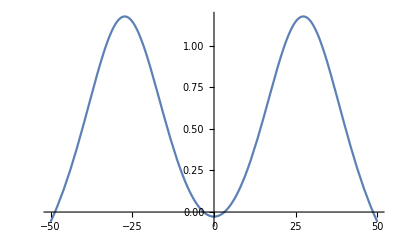

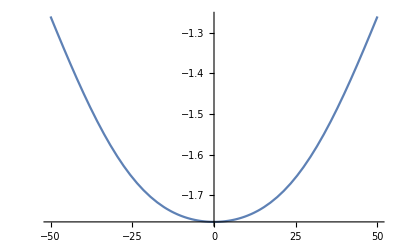

```mathematica
Plot[10^4 radFld[BiasCurvGrp,"bz",{0,0,z}],{z,-50,50},FrameLabel->{"Z [mm]","B_z [G]","X = Y = 0",""}]
Plot[10^4 radFld[AntiBiasCoil,"bz",{0,0,z}],{z,-50,50},
FrameLabel->{"Y [mm]","B_z [G]","X = Y = 0",""}]
```

#### Now fit near the trap center:

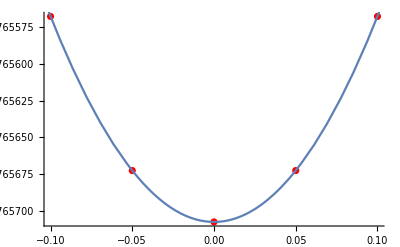

B_0 = -1.76571 G/A (just bias coil)

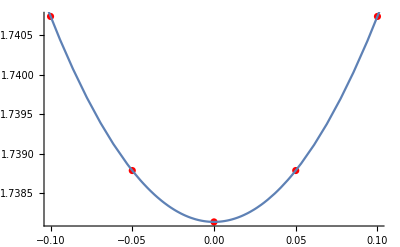

B_0 = 1.73813 G/A (just curvature coil)

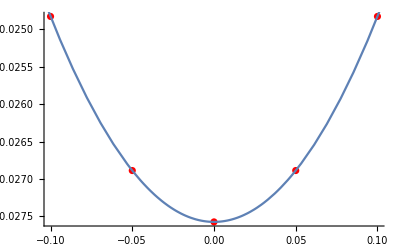

B'' = 0.549704 G/cm^2/A; offset at 200 A: -5.51492 G

```mathematica
tabbias = Table[{0.1ii,10^4 radFld[AntiBiasCoil,"bz",{0,0,ii}]},{ii,-1,1,0.5}];
fitbias = Fit[%,{1,x^2},x];
Show[ListPlot[tabbias, PlotStyle->Red], Plot[fitbias, {x, -0.2, 0.2}]]
Print["B_0", " = ",Coefficient[fitbias,x,0]," G/A (just bias coil)"]
tabcurv = Table[{0.1ii,10^4 radFld[CurvatureCoil,"bz",{0,0,ii}]},{ii,-1,1,0.5}];
fitcurv = Fit[%,{1,x^2},x];
Show[ListPlot[tabcurv, PlotStyle->Red], Plot[fitcurv, {x, -0.2, 0.2}]]
Print["B_0", " = ",Coefficient[fitcurv,x,0]," G/A (just curvature coil)"]
tabbiascurv = Table[{0.1ii,10^4 radFld[BiasCurvGrp,"bz",{0,0,ii}]},{ii,-1,1,0.5}];
fitbiascurv = Fit[%,{1,x^2},x];
Show[ListPlot[tabbiascurv, PlotStyle->Red], Plot[fitbiascurv, {x, -0.2, 0.2}]]
Print["B''", " = ",2*Coefficient[fitbiascurv,x,2]," G/cm^2/A; offset at 200 A: ", 200*Coefficient[fitbiascurv,x,0]," G"]
```

### Now, let’s see how things change if we use the curvature coils as MOT coils:

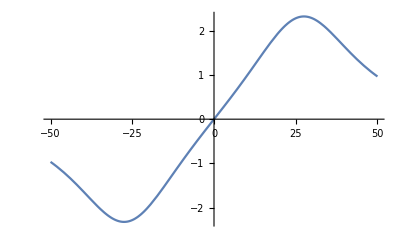

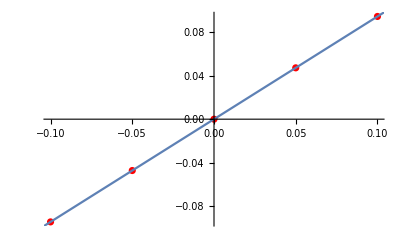

dB_z/dz = 0.942195 G/cm/A

```mathematica
CurvatureCoilasMOT =radObjCnt[{CurvatureCoilTop1BRASS,CurvatureCoilTop1,CurvatureCoilTop2BRASS,CurvatureCoilTop2}];
radTrfMlt[CurvatureCoilasMOT,PlaneSym,2];

Plot[10^4 radFld[CurvatureCoilasMOT,"bz",{0,0,z}],{z,-50,50},FrameLabel->{"Z [mm]","B_z [G]","X = Y = 0",""}]

tabcurvasMOT = Table[{0.1ii,10^4 radFld[CurvatureCoilasMOT,"bz",{0,0,ii}]},{ii,-1,1,0.5}];
fitcurvasMOT = Fit[%,{x},x];
Show[ListPlot[tabcurvasMOT, PlotStyle->Red], Plot[fitcurvasMOT, {x, -0.2, 0.2}]]
Print["dB_z/dz = ",Coefficient[fitcurvasMOT,x,1]," G/cm/A"]
```

### What about using the anti-bias coils as MOT coils?

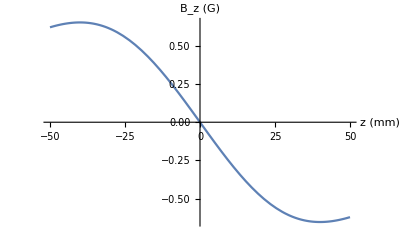

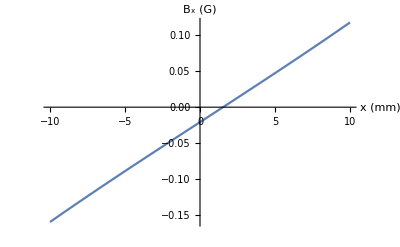

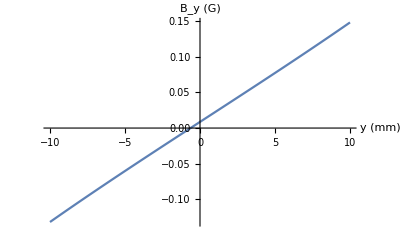

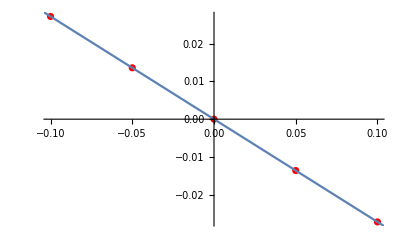

dB_z/dz = -0.272267 G/cm/A

```mathematica
Clear[AntiBiasasMOT,AntiBiasRods]
AntiBiasasMOT =radObjCnt[{AntiBiasCoilTop1BRASS,AntiBiasCoilTop1,AntiBiasCoilTop2BRASS,AntiBiasCoilTop2}];
AntiBiasRods=radObjCnt[{AntiBiasInTop,AntiBiasOutTop}];
radTrfOrnt[AntiBiasRods,RotInputTop];
MOTRodtrf=radTrfCmbL[PlaneSymAndCurrentInv,RotInputBot];
radTrfMlt[AntiBiasasMOT,PlaneSym,2];
radTrfMlt[AntiBiasRods,MOTRodtrf,2];
AntiBiasasMOT=radObjCnt[{AntiBiasasMOT,AntiBiasRods}];
Plot[10^4 radFld[AntiBiasasMOT,"bz",{0,0,z}],{z,-50,50},AxesLabel->{"z (mm)","B_z (G)"}]
Plot[10^4 radFld[AntiBiasasMOT,"bx",{x,0,0}],{x,-10,10},AxesLabel->{"x (mm)","B_x (G)"}]
Plot[10^4 radFld[AntiBiasasMOT,"by",{0,y,0}],{y,-10,10},AxesLabel->{"y (mm)","B_y (G)"}]
tabbiasasMOT = Table[{0.1ii,10^4 radFld[AntiBiasasMOT,"bz",{0,0,ii}]},{ii,-1,1,0.5}];
fitbiasasMOT = Fit[%,{x},x];
Show[ListPlot[tabbiasasMOT, PlotStyle->Red], Plot[fitbiasasMOT, {x, -0.2, 0.2}]]
Print["dB_z/dz = ",Coefficient[fitbiasasMOT,x,1]," G/cm/A"]
```

### What about making independent MOT coils?

Set it up:

```mathematica
rMOT1 = rcurv+rth+0.1*25.4;
rMOT2 = rcurv+2*(rth+0.1*25.4);

motturns = 9;

zoffmot = zoff+(Max[curvturns1,curvturns2,biasturns1,biasturns2]-motturns)*(zthcop+zsep);

MOTCoil1TopBRASS = radObjRaceTrk[{0.,0.,zoffmot+zthbrass/2},{rMOT1-rth/2,rMOT1+rth/2},{0.,0.},zthbrass,n,Icurv/zthbrass/rth];
MOTCoil1Top = radObjRaceTrk[{0.,0.,zoffmot+zthbrass+zsep+zthcop/2},{rMOT1-rth/2,rMOT1+rth/2},{0.,0.},zthcop,n,Icurv/zthcop/rth];
radTrfMlt[MOTCoil1Top,TransStackCoilsPos,motturns-1];

MOTCoil2TopBRASS = radObjRaceTrk[{0.,0.,zoffmot+zthbrass/2},{rMOT2-rth/2,rMOT2+rth/2},{0.,0.},zthbrass,n,Icurv/zthbrass/rth];
MOTCoil2Top = radObjRaceTrk[{0.,0.,zoffmot+zthbrass+zsep+zthcop/2},{rMOT2-rth/2,rMOT2+rth/2},{0.,0.},zthcop,n,Icurv/zthcop/rth];
radTrfMlt[MOTCoil2Top,TransStackCoilsPos,motturns-1];

MOTCoils = radObjCnt[{MOTCoil1TopBRASS,MOTCoil1Top,MOTCoil2TopBRASS,MOTCoil2Top}];

PlaneSym = radTrfPlSym[{0,0,0},{0,0,1}];

radTrfMlt[MOTCoils,PlaneSym,2];

Show[Graphics3D[radObjDrw[MOTCoils],PlotLabel->"MOT Coils",BaseStyle->{14,FontFamily->"Times"}]]'
Show[Graphics3D[radObjDrw[radObjCnt[{MOTCoils,BiasCurvGrp}]],PlotLabel->"MOT Coils + Ioffe Coils",BaseStyle->{14,FontFamily->"Times"}]]'
```

-Graphics3D-'

-Graphics3D-'

Now fit it:

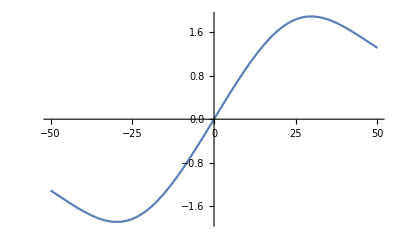

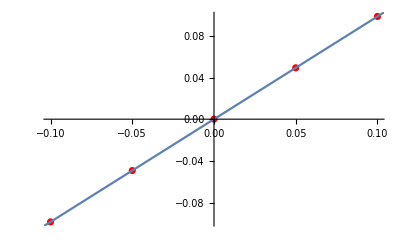

dB_z/dz = 0.986178 G/cm/A

```mathematica
Plot[10^4 radFld[MOTCoils,"bz",{0,0,z}],{z,-50,50},FrameLabel->{"Z [mm]","B_z [G]","X = Y = 0",""}]

tabMOT = Table[{0.1ii,10^4 radFld[MOTCoils,"bz",{0,0,ii}]},{ii,-1,1,0.5}];
fitMOT = Fit[%,{x},x];
Show[ListPlot[tabMOT, PlotStyle->Red], Plot[fitMOT, {x, -0.2, 0.2}]]
Print[Subscript[dB, z]/dz," = ",Coefficient[fitMOT,x,1]," G/cm/A"]
```

### Now make original cloverleaf coil:

```mathematica
(* Now, let's make an independent radius for the clover leaf coils *)
(*rclovermax = r2+1/2+3/2rth*)
rclovermax=4*25.4-rth/2
zcloveroff = zoff+(Max[curvturns1,biasturns1,curvturns2,biasturns2]-1)*(zthcop+zsep)+zthbrass+3*zsep;
csep = 0.1*25.4;

colorclover = {0,1,0};

gradturns = 18; (* How many turns *)

Iclover = 1;

(* For the clover leaf coils, we need, rotate by 45 degrees: *)
RotTrans45= radTrfRot[{0,0,0},{0,0,1},π/4];
RotTrans23= radTrfRot[{0,0,0},{0,0,1},-π/8];
RotTrans90 = radTrfRot[{0,0,0},{0,0,1},π/2];
CurrentInv = radTrfInv[];

(* Combine the two symmetries: *)
radTrfCmbR[RotTrans45,CurrentInv];
radTrfCmbR[RotTrans90,CurrentInv];

θ2 = 22.5 π/180;
nseg = 7;
dr = rth/nseg;

(* To calculate the current distribution more accurately, divide up the clovers into smaller pieces *)
For[i=-Floor[nseg/2],i<Ceiling[nseg/2]+1,i++,
xmin = NSolve[(rcurv+i dr)^2== x^2+(-x Tan[θ2]+csep/Cos[θ2])^2,{x}];
θ3 = ArcTan[(x Tan[θ2]-csep/Cos[θ2])/x]/.{xmin[[2]][[1]]};
If[Abs[ArcSin[i dr/(rcurv+i dr)]]<θ3,
(* Not going to overlap with neighboring coil? *)
CloverCoilArc1 = radObjArcCur[{0.,0.,zcloveroff+zthcop/2},{rcurv+i dr-dr/2,rcurv+i dr+dr/2},{0+ArcSin[i dr/(rcurv+i dr)],π/4-ArcSin[i dr/(rcurv+i dr)]},zthcop,n,Iclover/zthcop/rth];

CloverCoilArc2 = radObjArcCur[{0.,0.,zcloveroff+zthcop/2},{rclovermax-i dr-dr/2,rclovermax-i dr +dr/2},{0+ArcSin[i dr/(rclovermax-i dr)],π/4-ArcSin[i dr/(rclovermax-i dr)]},zthcop,n,-Iclover/zthcop/rth];

x1 = √((rcurv+i dr)^2-(i dr)^2);
x2 = √((rclovermax-i dr)^2-(i dr)^2);

CloverCoilLead = radObjRecCur[{(x1+x2)/2,i dr,zcloveroff+zthcop/2},{x2-x1,dr,zthcop},{-Iclover/zthcop/rth,0,0}];
,
(* Going to overlap with neighboring coil (cut it short): *) 
CloverCoilArc1 = radObjArcCur[{0.,0.,zcloveroff+zthcop/2},{rcurv+i dr-dr/2,rcurv+i dr+dr/2},{0-θ3,π/4+θ3},zthcop,n,Iclover/rth/zthcop];
CloverCoilArc2 = radObjArcCur[{0.,0.,zcloveroff+zthcop/2},{rclovermax-i dr-dr/2,rclovermax-i dr +dr/2},{0+ArcSin[i dr/(rclovermax-i dr)],π/4-ArcSin[i dr/(rclovermax-i dr)]},zthcop,n,-Iclover/rth/zthcop];

x1 =-( i dr - csep/Cos[θ2])/Tan[θ2];
x2 = √((rclovermax-i dr)^2-(i dr)^2);

CloverCoilLead1 = radObjRecCur[{(x1+x2)/2,i dr,zcloveroff+zthcop/2},{x2-x1,dr,zthcop},{-Iclover/rth/zthcop ,0,0}];

x2 = x1;
x1 = (rcurv+i dr)Cos[θ3];
y1 = -Tan[θ2]x1+ csep/Cos[θ2];
y2 = -Tan[θ2]x2 + csep/Cos[θ2];
L = Sqrt[(x2-x1)^2+(y2-y1)^2];

RotLead= radTrfRot[{x1,y1,0},{0,0,1},-θ2];
CloverCoilLead2 = radObjRecCur[{x1+L/2,y1,zcloveroff+zthcop/2},{L,dr,zthcop},{-Iclover/rth/zthcop,0,0}];
radTrfMlt[CloverCoilLead2,RotLead,1];
CloverCoilLead = radObjCnt[{CloverCoilLead1,CloverCoilLead2}]
];

RotLead= radTrfRot[{0,0,0},{0,0,1},π/4];
MirrorLead = radTrfPlSym[{0,0,0},{0,1,0}];

radTrfCmbR[RotLead,MirrorLead];
radTrfMlt[CloverCoilLead,RotLead,2];

(* Group together the parts of the clover coil *)
If[i==-Floor[nseg/2],
CloverCoil = radObjCnt[{CloverCoilArc1,CloverCoilArc2,CloverCoilLead}],
CloverCoil = radObjCnt[{CloverCoil,CloverCoilArc1,CloverCoilArc2,CloverCoilLead}];
];
];
radObjDrwAtr[CloverCoil,colorclover,0.001];

(* Now that we have one complete clover coil, let's rotate by 45 degrees: *)
radTrfOrnt[CloverCoil,RotTrans23];
radTrfMlt[CloverCoil,RotTrans90,4];

(* Now, let's do the translation to make the coils themselves: *)
TransStackCoils =radTrfTrsl[{0,0,zthcop+zsep}];
radTrfMlt[CloverCoil,TransStackCoils,gradturns];

(* Now, we mirror around the z plane: *)
MirrorSym = radTrfPlSym[{0,0,0},{0,0,1}];
radTrfMlt[CloverCoil,MirrorSym,2];
```

95.25

#### Plot ‘er up

```mathematica
Show[Graphics3D[radObjDrw[CloverCoil],PlotLabel->"Clover Leaf Coils",BaseStyle->{14,FontFamily->"Times"}]]'
```

-Graphics3D-'

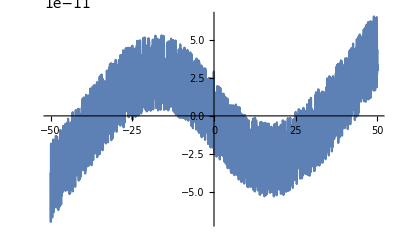

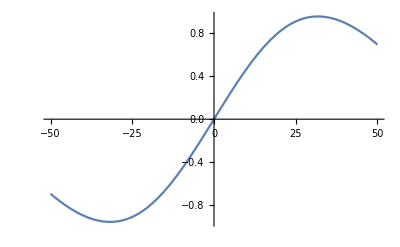

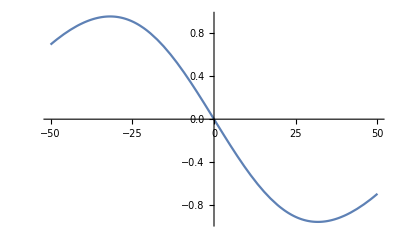

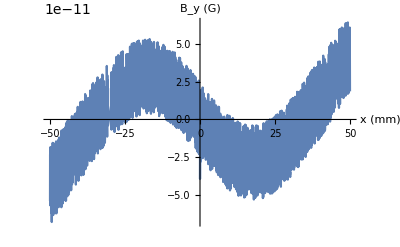

```mathematica
Plot[10^4 radFld[CloverCoil,"bx",{0,y,0}],{y,-50,50},
FrameLabel->{"y (mm)","B_x (G)"}]
Plot[10^4 radFld[CloverCoil,"by",{0,y,0}],{y,-50,50},
FrameLabel->{"y (mm)","B_y (G)"}]
Plot[10^4 radFld[CloverCoil,"bx",{x,0,0}],{x,-50,50},
FrameLabel->{"x (mm)","B_x (G)"}]
Plot[10^4 radFld[CloverCoil,"by",{x,0,0}],{x,-50,50},
AxesLabel->{"x (mm)","B_y (G)"}]
```

#### Fit to get out the gradient:

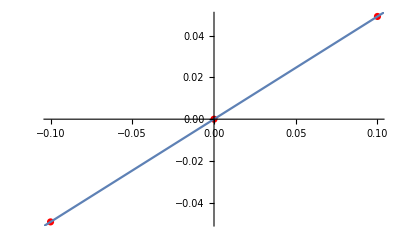

dB_y/dy = 0.492592 G/cm/A

```mathematica
tabclover=Table[{0.1ii,10^4 radFld[CloverCoil,"by",{0,ii,0}]},{ii,-1,1,1}];
fitclover = Fit[%,{1,x,x^2},x];
Show[ListPlot[tabclover, PlotStyle->Red], Plot[fitclover, {x, -0.2, 0.2}]]
Print["dB_y/dy = ",Coefficient[fitclover,x,1]," G/cm/A"]
```

### Now make cloverleaf coil with thick brass top and bottom:

```mathematica
(* Now, let's make an independent radius for the clover leaf coils *)
(*rclovermax = r2+1/2+3/2rth*)
rclovermax=4*25.4-rth/2
zcloveroff = zoff+(Max[(curvturns1-1)*(zthcop+zsep)+zsep,(biasturns1-1)*(zthcop+zsepbias)+zsepbias,(curvturns2-1)*(zthcop+zsep)+zsep,(biasturns2-1)*(zthcop+zsepbias)+zsepbias])+zthbrass+zsep+1/32*25.4;(* G10 sheet is 1/32" thick*)
csep = 0.1*25.4;
cloverBrassThk=3; (*Set top and bottom brass layers to 3mm thickness to equalize resistance with the copper layers*)

colorclover = {0,1,0};
colorcloverBrass={0.33,1,0.33};

gradturns = 18; (* How many turns *)

Iclover = 1;

(* For the clover leaf coils, we need, rotate by 45 degrees: *)
RotTrans45= radTrfRot[{0,0,0},{0,0,1},π/4];
RotTrans23= radTrfRot[{0,0,0},{0,0,1},-π/8];
RotTrans90 = radTrfRot[{0,0,0},{0,0,1},π/2];
CurrentInv = radTrfInv[];

(* Combine the two symmetries: *)
radTrfCmbR[RotTrans45,CurrentInv];
radTrfCmbR[RotTrans90,CurrentInv];

θ2 = 22.5 π/180;
nseg = 7;
dr = rth/nseg;

(*Begin by making the brass layers*)

(* To calculate the current distribution more accurately, divide up the clovers into smaller pieces *)
For[i=-Floor[nseg/2],i<Ceiling[nseg/2]+1,i++,
xmin = NSolve[(rcurv+i dr)^2== x^2+(-x Tan[θ2]+csep/Cos[θ2])^2,{x}];
θ3 = ArcTan[(x Tan[θ2]-csep/Cos[θ2])/x]/.{xmin[[2]][[1]]};
If[Abs[ArcSin[i dr/(rcurv+i dr)]]<θ3,
(* Not going to overlap with neighboring coil? *)
CloverCoilArc1 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk/2},{rcurv+i dr-dr/2,rcurv+i dr+dr/2},{0+ArcSin[i dr/(rcurv+i dr)],π/4-ArcSin[i dr/(rcurv+i dr)]},cloverBrassThk,n,Iclover/cloverBrassThk/rth];

CloverCoilArc2 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk/2},{rclovermax-i dr-dr/2,rclovermax-i dr +dr/2},{0+ArcSin[i dr/(rclovermax-i dr)],π/4-ArcSin[i dr/(rclovermax-i dr)]},cloverBrassThk,n,-Iclover/cloverBrassThk/rth];

x1 = √((rcurv+i dr)^2-(i dr)^2);
x2 = √((rclovermax-i dr)^2-(i dr)^2);

CloverCoilLead = radObjRecCur[{(x1+x2)/2,i dr,zcloveroff+cloverBrassThk/2},{x2-x1,dr,cloverBrassThk},{-Iclover/cloverBrassThk/rth,0,0}];
,
(* Going to overlap with neighboring coil (cut it short): *) 
CloverCoilArc1 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk/2},{rcurv+i dr-dr/2,rcurv+i dr+dr/2},{0-θ3,π/4+θ3},cloverBrassThk,n,Iclover/rth/cloverBrassThk];
CloverCoilArc2 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk/2},{rclovermax-i dr-dr/2,rclovermax-i dr +dr/2},{0+ArcSin[i dr/(rclovermax-i dr)],π/4-ArcSin[i dr/(rclovermax-i dr)]},cloverBrassThk,n,-Iclover/rth/cloverBrassThk];

x1 =-( i dr - csep/Cos[θ2])/Tan[θ2];
x2 = √((rclovermax-i dr)^2-(i dr)^2);

CloverCoilLead1 = radObjRecCur[{(x1+x2)/2,i dr,zcloveroff+cloverBrassThk/2},{x2-x1,dr,cloverBrassThk},{-Iclover/rth/cloverBrassThk ,0,0}];

x2 = x1;
x1 = (rcurv+i dr)Cos[θ3];
y1 = -Tan[θ2]x1+ csep/Cos[θ2];
y2 = -Tan[θ2]x2 + csep/Cos[θ2];
L = Sqrt[(x2-x1)^2+(y2-y1)^2];

RotLead= radTrfRot[{x1,y1,0},{0,0,1},-θ2];
CloverCoilLead2 = radObjRecCur[{x1+L/2,y1,zcloveroff+cloverBrassThk/2},{L,dr,cloverBrassThk},{-Iclover/rth/cloverBrassThk,0,0}];
radTrfMlt[CloverCoilLead2,RotLead,1];
CloverCoilLead = radObjCnt[{CloverCoilLead1,CloverCoilLead2}]
];

RotLead= radTrfRot[{0,0,0},{0,0,1},π/4];
MirrorLead = radTrfPlSym[{0,0,0},{0,1,0}];

radTrfCmbR[RotLead,MirrorLead];
radTrfMlt[CloverCoilLead,RotLead,2];

(* Group together the parts of the clover coil *)
If[i==-Floor[nseg/2],
CloverCoilBrass = radObjCnt[{CloverCoilArc1,CloverCoilArc2,CloverCoilLead}],
CloverCoilBrass = radObjCnt[{CloverCoilBrass,CloverCoilArc1,CloverCoilArc2,CloverCoilLead}];
];
];
radObjDrwAtr[CloverCoilBrass,colorcloverBrass,0.001];

(*Fill in the copper layers in between*)

(* To calculate the current distribution more accurately, divide up the clovers into smaller pieces *)
For[i=-Floor[nseg/2],i<Ceiling[nseg/2]+1,i++,
xmin = NSolve[(rcurv+i dr)^2== x^2+(-x Tan[θ2]+csep/Cos[θ2])^2,{x}];
θ3 = ArcTan[(x Tan[θ2]-csep/Cos[θ2])/x]/.{xmin[[2]][[1]]};
If[Abs[ArcSin[i dr/(rcurv+i dr)]]<θ3,
(* Not going to overlap with neighboring coil? *)
CloverCoilArc1 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk+zsep+zthcop/2},{rcurv+i dr-dr/2,rcurv+i dr+dr/2},{0+ArcSin[i dr/(rcurv+i dr)],π/4-ArcSin[i dr/(rcurv+i dr)]},zthcop,n,Iclover/zthcop/rth];

CloverCoilArc2 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk+zsep+zthcop/2},{rclovermax-i dr-dr/2,rclovermax-i dr +dr/2},{0+ArcSin[i dr/(rclovermax-i dr)],π/4-ArcSin[i dr/(rclovermax-i dr)]},zthcop,n,-Iclover/zthcop/rth];

x1 = √((rcurv+i dr)^2-(i dr)^2);
x2 = √((rclovermax-i dr)^2-(i dr)^2);

CloverCoilLead = radObjRecCur[{(x1+x2)/2,i dr,zcloveroff+cloverBrassThk+zsep+zthcop/2},{x2-x1,dr,zthcop},{-Iclover/zthcop/rth,0,0}];
,
(* Going to overlap with neighboring coil (cut it short): *) 
CloverCoilArc1 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk+zsep+zthcop/2},{rcurv+i dr-dr/2,rcurv+i dr+dr/2},{0-θ3,π/4+θ3},zthcop,n,Iclover/rth/zthcop];
CloverCoilArc2 = radObjArcCur[{0.,0.,zcloveroff+cloverBrassThk+zsep+zthcop/2},{rclovermax-i dr-dr/2,rclovermax-i dr +dr/2},{0+ArcSin[i dr/(rclovermax-i dr)],π/4-ArcSin[i dr/(rclovermax-i dr)]},zthcop,n,-Iclover/rth/zthcop];

x1 =-( i dr - csep/Cos[θ2])/Tan[θ2];
x2 = √((rclovermax-i dr)^2-(i dr)^2);

CloverCoilLead1 = radObjRecCur[{(x1+x2)/2,i dr,zcloveroff+cloverBrassThk+zsep+zthcop/2},{x2-x1,dr,zthcop},{-Iclover/rth/zthcop ,0,0}];

x2 = x1;
x1 = (rcurv+i dr)Cos[θ3];
y1 = -Tan[θ2]x1+ csep/Cos[θ2];
y2 = -Tan[θ2]x2 + csep/Cos[θ2];
L = Sqrt[(x2-x1)^2+(y2-y1)^2];

RotLead= radTrfRot[{x1,y1,0},{0,0,1},-θ2];
CloverCoilLead2 = radObjRecCur[{x1+L/2,y1,zcloveroff+cloverBrassThk+zsep+zthcop/2},{L,dr,zthcop},{-Iclover/rth/zthcop,0,0}];
radTrfMlt[CloverCoilLead2,RotLead,1];
CloverCoilLead = radObjCnt[{CloverCoilLead1,CloverCoilLead2}]
];

RotLead= radTrfRot[{0,0,0},{0,0,1},π/4];
MirrorLead = radTrfPlSym[{0,0,0},{0,1,0}];

radTrfCmbR[RotLead,MirrorLead];
radTrfMlt[CloverCoilLead,RotLead,2];

(* Group together the parts of the clover coil *)
If[i==-Floor[nseg/2],
CloverCoil = radObjCnt[{CloverCoilArc1,CloverCoilArc2,CloverCoilLead}],
CloverCoil = radObjCnt[{CloverCoil,CloverCoilArc1,CloverCoilArc2,CloverCoilLead}];
];
];
radObjDrwAtr[CloverCoil,colorclover,0.001];

(* Now, let's do the translation to make the coils themselves: *)

(* Copper turns first: *)
TransStackCoils =radTrfTrsl[{0,0,zthcop+zsep}];
radTrfMlt[CloverCoil,TransStackCoils,gradturns-2];
(* Brass Turns Second: *)
TransStackBrass =radTrfTrsl[{0,0,cloverBrassThk+zsep+(gradturns-2) (zthcop+zsep)}];
radTrfMlt[CloverCoilBrass,TransStackBrass,2];

(*Combine the Brass and Copper Coils*)
CloverCoil = radObjCnt[{CloverCoil,CloverCoilBrass}];

(* Now that we have one complete clover coil, let's rotate by 45 degrees: *)
radTrfOrnt[CloverCoil,RotTrans23];
radTrfMlt[CloverCoil,RotTrans90,4];

(* Now, we mirror around the z plane: *)
MirrorSym = radTrfPlSym[{0,0,0},{0,0,1}];
radTrfMlt[CloverCoil,MirrorSym,2];
```

95.25

#### Plot ‘er up

```mathematica
Show[Graphics3D[radObjDrw[CloverCoil],PlotLabel->"Clover Leaf Coils",BaseStyle->{14,FontFamily->"Times"}]]'
```

-Graphics3D-'

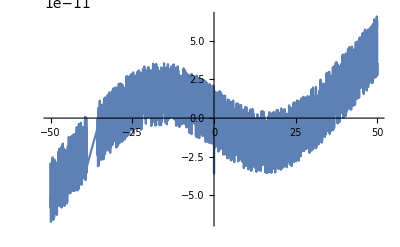

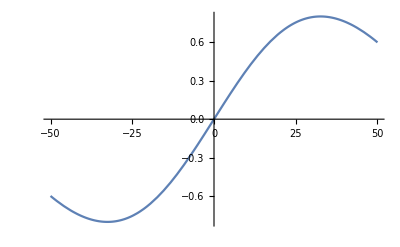

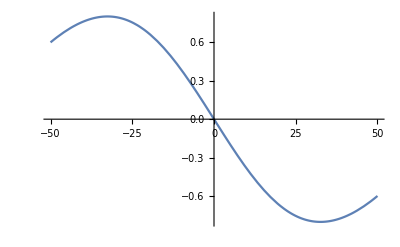

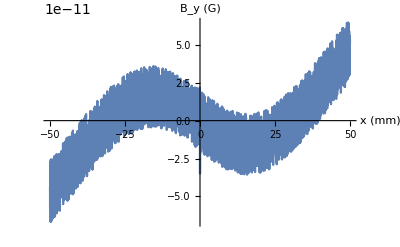

```mathematica
Plot[10^4 radFld[CloverCoil,"bx",{0,y,0}],{y,-50,50},
FrameLabel->{"y (mm)","B_x (G)"}]
Plot[10^4 radFld[CloverCoil,"by",{0,y,0}],{y,-50,50},
FrameLabel->{"y (mm)","B_y (G)"}]
Plot[10^4 radFld[CloverCoil,"bx",{x,0,0}],{x,-50,50},
FrameLabel->{"x (mm)","B_x (G)"}]
Plot[10^4 radFld[CloverCoil,"by",{x,0,0}],{x,-50,50},
AxesLabel->{"x (mm)","B_y (G)"}]
```

#### Fit to get out the gradient:

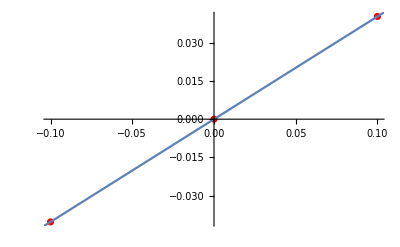

dB_y/dy = 0.403262 G/cm/A

```mathematica
tabclover=Table[{0.1ii,10^4 radFld[CloverCoil,"by",{0,ii,0}]},{ii,-1,1,1}];
fitclover = Fit[%,{1,x,x^2},x];
Show[ListPlot[tabclover, PlotStyle->Red], Plot[fitclover, {x, -0.2, 0.2}]]
Print["dB_y/dy = ",Coefficient[fitclover,x,1]," G/cm/A"]
```

### Now render everything together:

```mathematica
Show[Graphics3D[radObjDrw[radObjCnt[{BiasCurvGrp,CloverCoil}]],PlotLabel->"Clover Leaf Trap",BaseStyle->{14,FontFamily->"Times"}]]'
```

-Graphics3D-'

### Comparison w/ Stamper-Kurn Thesis

```mathematica
mLi=7.016004 1.66054*^-27;
mRb=86.909180 1.66054*^-27;
μb=9.274009*^-24;
kb=1.38*^-23;
Bpp=2*Coefficient[fitbiascurv,x,2]*10^-4/(10^-4); (*T/m^2/A*)
Bp=Coefficient[fitclover,x,1]*10^-4/(10^-2);(*T/m/A*)
Bbb=Abs[Coefficient[fitbias,x,0]];(* G/A *)
Bbc=Abs[Coefficient[fitcurv,x,0]];(* G/A *)
ωr[B0_,Bp_,Bpp_,m_]:=Sqrt[μb (Bp^2/B0-Bpp/2)/m];
ωz[Bpp_,m_]:=Sqrt[μb Bpp/m];
Zinst[B0_,Bp_,Bpp_]:=Bp/Bpp-0.5 B0/Bp;
Bppr[B0_,Bp_,Bpp_]:=(Bp^2/B0-Bpp/2);
```

```mathematica
ωr[1 10^-4,220 Bp,300 Bpp,mLi]/(2 π)
ωz[300 Bpp,mLi]/(2 π)
ωr[1 10^-4,220 Bp,300 Bpp,mRb]/(2 π)
ωz[300 Bpp,mRb]/(2 π)
```

439.649

58.4096

124.916

16.5957

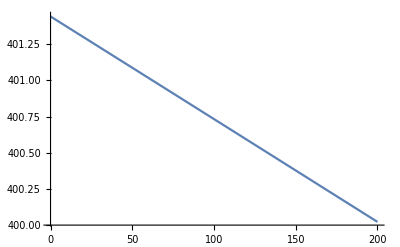

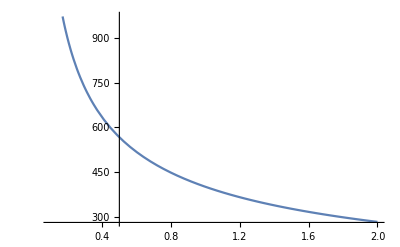

```mathematica
Plot[ωr[1 10^-4,200 Bp,curr Bpp,mLi]/(2 π),{curr,0,200}]
Plot[ωr[bias 10^-4,200 Bp,200 Bpp,mLi]/(2 π),{bias,0.1,2}]
```

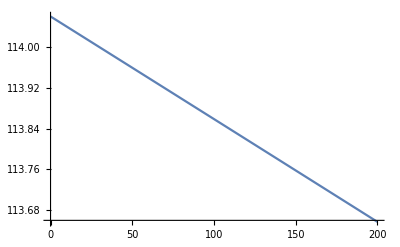

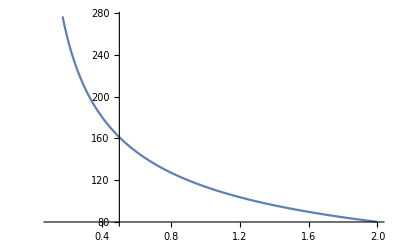

```mathematica
Plot[ωr[1 10^-4,200 Bp,curr Bpp,mRb]/(2 π),{curr,0,200}]
Plot[ωr[bias 10^-4,200 Bp,200 Bpp,mRb]/(2 π),{bias,0.1,2}]
```

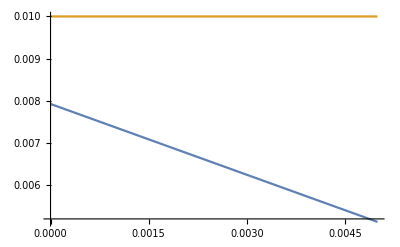

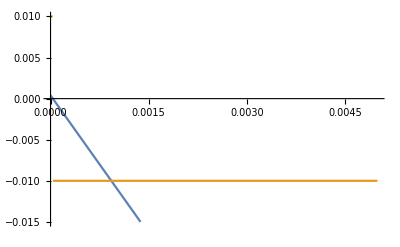

```mathematica
Plot[{Zinst[B0,200 Bp,200 Bpp],Sign[Bppr[B0,200 Bp,200 Bpp]]/100},{B0,0,50 10^-4}]
Plot[{Zinst[B0,10 Bp,200 Bpp],Sign[Bppr[B0,10 Bp,200 Bpp]]/100},{B0,0,50 10^-4},PlotRange->{-0.015,0.01}]
```

```mathematica
(*Mode matching calculations from Ketterle's Varenna notes and D. S.-K. thesis*)
(*Using numbers from DSK thesis for temp/rad.*)
T=100*^-6;(*Approx. temp for Na out of MOT, K*)
r0=1.1*^-3;(*Approx. MOT radius, m*)
B00 = kb*T/(μb/10^4);(*Min bias field, G*)
Print["Minimum Bias: ", B00, " G"]
(*Mode matching only works if B_bias > B00*)
sf =40; (*safety factor to ensure B_bias >> B00*)
Print["Safe Bias: ", sf*B00, " G"]
k0=kb*T/(100 r0)^2;(*J/cm^2, this is the necessary trap stiffness*)
BzzLoad=k0/(μb/10^4);(*G/cm^2, Eq. 10 in Varenna notes*)
IzzLoad=BzzLoad/Bpp; (* No conversion factor because T/m^2 = G/cm^2*)
BrrLoad=Sqrt[3 k0/(2 μb/10^4) B00 sf] ;(*Eq. 11 in Varenna notes*)
IrrLoad=BrrLoad/(100Bp); (*100 converts from T/m to G/cm*)
zin=Sqrt[sf B00*(3 k0/(2 μb/10^4))^-1]/(100r0); (*instab. dist in r0*)
IbbLoad=Bbc*IzzLoad/Bbb-sf B00/Bbb;
Print["(I_ab, I_curv, I_clover) = (", IbbLoad,",",IzzLoad,",",IrrLoad,")"]
```

Minimum Bias: 1.48803 G

Safe Bias: 59.5212 G

(I_ab, I_curv, I_clover) = (186.513,223.716,259.841)

```mathematica
(*Mode matching calculations from Ketterle's Varenna notes and D. S.-K. thesis*)
(*Assuming D1 cooling of Li*)
T=50*^-6;(*Approx. temp for Li out of MOT, K*)
r0=0.7*^-3;(*Approx. MOT radius, m*)
B00 = kb*T/(μb/10^4);(*Min bias field, G*)
Print["Minimum Bias: ", B00, " G"]
(*Mode matching only works if B_bias > B00*)
sf =40; (*safety factor to ensure B_bias >> B00*)
(*sf = 40 gives instability distance of 5*r0*)
Print["Safe Bias: ", sf*B00, " G"]
k0=kb*T/(100 r0)^2;(*J/cm^2, this is the necessary trap stiffness*)
BzzLoad=k0/(μb/10^4);(*G/cm^2, Eq. 10 in Varenna notes*)
IzzLoad=BzzLoad/Bpp; (* No conversion factor because T/m^2 = G/cm^2*)
BrrLoad=Sqrt[3 k0/(2 μb/10^4) B00 sf]; (*Eq. 11 in Varenna notes*)
IrrLoad=BrrLoad/(100Bp); (*100 converts from T/m to G/cm*)
zin=Sqrt[sf B00*(3 k0/(2 μb/10^4))^-1]/(100r0); (*instab. dist in r0*)
IbbLoad=Bbc*IzzLoad/Bbb-sf B00/Bbb;
Print["(I_ab, I_curv, I_clover) = (", IbbLoad,",",IzzLoad,",",IrrLoad,")"]
```

Minimum Bias: 0.744015 G

Safe Bias: 29.7606 G

(I_ab, I_curv, I_clover) = (255.053,276.221,204.161)

### Cooling Calculations

```mathematica
Clear[Δp,ρc,ρw,Cv,μ,h,k,α,Θcm,xstar,xstar2,xstar3,u,L,pd,Rhyd,Rhyd2,Rat,Rat2,Rat3];
```

```mathematica
(*constants*)
Δp=0.5 6894.76;(* Pressure differential in N/m^2 *)
ρc=1.68*^-8; (* Ω*m *)
ρw=1000;(* kg/m^3, water mass density *)
Cv=4.186 10^3;(* J/kg/K, specific heat of water assuming Cp=Cv since liquids are incompressible *)
μ=1.002 10^-3;(* N*s/m^2, dynamic viscosity of water *)
h=0.254 10^-3;(* m, cooling channel height *)
k=0.58;(* W/(m*K), Thermal Conductivity of Water *)
α=k/(Cv ρw);(* Coefficient for the Heat Equation *)
```

```mathematica
(*Helper functions*)
Θcm[xstar_]:=0.91 Exp[-2 2.83 xstar/3]+0.053 Exp[-2 32.1 xstar/3]+0.015 Exp[-2 93.4 xstar/3];(*Final relative temperature*)
L[r_]:=2 π r (1/8);(*channel length*)
pd[L_,u_,w_]:=(12 L u μ/(h^2 (1-.63 h/w)))/6894.76;
Rhyd[L_,w_]:=(12 L μ/(w h^3 (1-.63 h/w)));
Rhyd2[L_,w_]:=(12 L μ/(w h^3));
xstar[L_,w_]:=4 w α L Rhyd[L,w]/(h Δp);(*scaled length coordinate*)
xstar2[L_,w_,Δp_]:=4 w α L Rhyd2[L,w]/(h Δp);
xstar3[L_,w_,Δp_]:=4 w α L Rhyd[L,w]/(h Δp);
u[R_,w_]:=Δp/(R h w);(*average flow velocity*)
Rat[r_,w_]:=2 L[r] Rhyd[L[r],w]/(1-Θcm[xstar[L[r],w]]);
Rat2[r_,w_,Δp_]:=2 L[r] Rhyd2[L[r],w]/(1-Θcm[xstar2[L[r],w,Δp]]);
Rat3[r_,w_,Δp_]:=2 L[r] Rhyd[L[r],w]/(1-Θcm[xstar3[L[r],w,Δp]]);
```

```mathematica
Lchin=45*^-3;
Wchin=6.35*^-3;
Rchin=Rhyd[Lchin,Wchin]
u[Rchin,Wchin]
xchin=xstar[Lchin,Wchin]
Θcm[xchin]
```

5.33422×10^9

0.400692

0.964769

0.147414

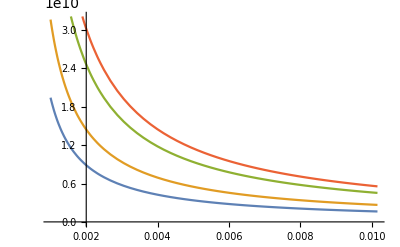

```mathematica
(*Hydraulic Resistance for each coil*)
Plot[{Rhyd[rcurv 10^-3,w],Rhyd[(rcurv+rspac+rth) 10^-3,w],Rhyd[rbias 10^-3,w],Rhyd[(rbias+rspac+rth) 10^-3,w]},{w,.001,.4*25.4*^-3}]
```

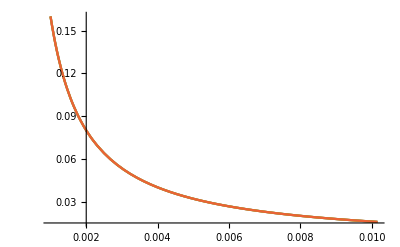

```mathematica
Plot[{(Rhyd[rcurv 10^-3,w]-Rhyd2[rcurv 10^-3,w])/Rhyd[rcurv 10^-3,w],(Rhyd[(rcurv+rspac+rth) 10^-3,w]-Rhyd2[(rcurv+rspac+rth) 10^-3,w])/Rhyd[(rcurv+rspac+rth) 10^-3,w],(Rhyd[rbias 10^-3,w]-Rhyd2[rbias 10^-3,w])/Rhyd[rbias 10^-3,w],(Rhyd[(rbias+rspac+rth) 10^-3,w]-Rhyd2[(rbias+rspac+rth) 10^-3,w])/Rhyd[(rbias+rspac+rth) 10^-3,w]},{w,.001,.4*25.4*^-3}]
```

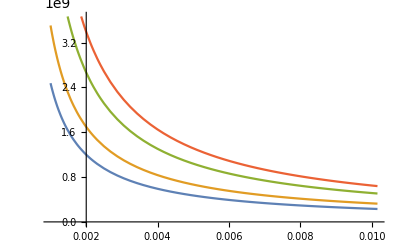

```mathematica
Plot[{Rat[rcurv 10^-3,w],Rat[(rcurv+rspac+rth) 10^-3,w],Rat[rbias 10^-3,w],Rat[(rbias+rspac+rth) 10^-3,w]},{w,.001,.4*25.4*^-3}]
```

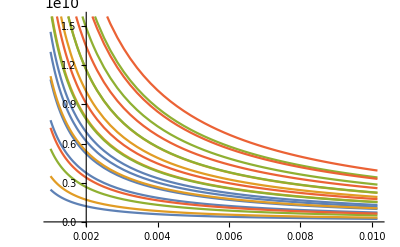

```mathematica
Plot[{Table[Rat3[rcurv 10^-3,w,i 6894.76],{i,1,21,5}],Table[Rat3[(rcurv+rspac+rth) 10^-3,w,i 6894.76],{i,1,21,5}],Table[Rat3[rbias 10^-3,w,i 6894.76],{i,1,21,5}],Table[Rat3[(rbias+rspac+rth) 10^-3,w,i 6894.76],{i,1,21,5}]},{w,.001,.4*25.4*^-3}]
```

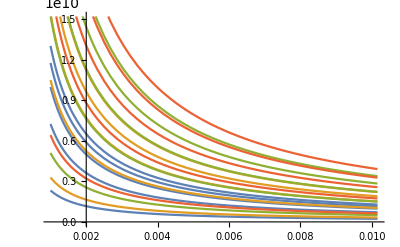

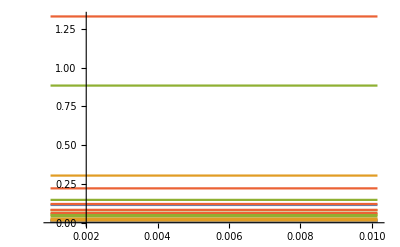

```mathematica
Plot[{Table[Rat2[rcurv 10^-3,w,i 6894.76],{i,1,21,5}],Table[Rat2[(rcurv+rspac+rth) 10^-3,w,i 6894.76],{i,1,21,5}],Table[Rat2[rbias 10^-3,w,i 6894.76],{i,1,21,5}],Table[Rat2[(rbias+rspac+rth) 10^-3,w,i 6894.76],{i,1,21,5}]},{w,.001,.4*25.4*^-3}]
Plot[{Table[xstar2[rcurv 10^-3,w,i 6894.76],{i,1,21,5}],Table[xstar2[(rcurv+rspac+rth) 10^-3,w,i 6894.76],{i,1,21,5}],Table[xstar2[rbias 10^-3,w,i 6894.76],{i,1,21,5}],Table[xstar2[(rbias+rspac+rth) 10^-3,w,i 6894.76],{i,1,21,5}]},{w,.001,.4*25.4*^-3},PlotRange->All]
```

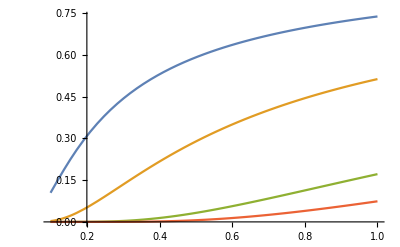

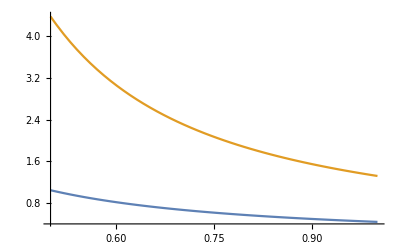

```mathematica
Plot[{Θcm[xstar2[rcurv 10^-3,w,p 6894.76]],Θcm[xstar2[(rcurv+rspac+rth) 10^-3,w,p 6894.76]],Θcm[xstar2[rbias 10^-3,w,p 6894.76]],Θcm[xstar2[(rbias+rspac+rth) 10^-3,w,p 6894.76]]},{p,.1,1},PlotRange->All]
Plot[{(Θcm[xstar2[rcurv 10^-3,w,p 6894.76]]-Θcm[xstar2[(rcurv+rspac+rth) 10^-3,w,p 6894.76]])/Θcm[xstar2[(rcurv+rspac+rth) 10^-3,w,p 6894.76]],(Θcm[xstar2[rbias 10^-3,w,p 6894.76]]-Θcm[xstar2[(rbias+rspac+rth) 10^-3,w,p 6894.76]])/Θcm[xstar2[(rbias+rspac+rth) 10^-3,w,p 6894.76]]},{p,.5,1}]
```

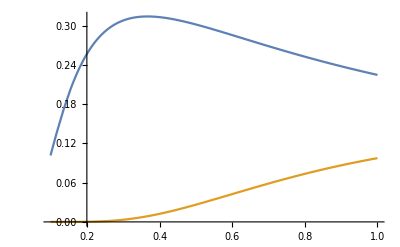

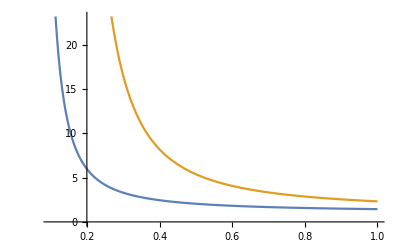

```mathematica
Plot[{Θcm[xstar2[rcurv 10^-3,w,p 6894.76]]-Θcm[xstar2[(rcurv+rspac+rth) 10^-3,w,p 6894.76]],Θcm[xstar2[rbias 10^-3,w,p 6894.76]]-Θcm[xstar2[(rbias+rspac+rth) 10^-3,w,p 6894.76]]},{p,.1,1}]
Plot[{(Θcm[xstar2[rcurv 10^-3,w,p 6894.76]]/Θcm[xstar2[(rcurv+rspac+rth) 10^-3,w,p 6894.76]]),(Θcm[xstar2[rbias 10^-3,w,p 6894.76]]/Θcm[xstar2[(rbias+rspac+rth) 10^-3,w,p 6894.76]])},{p,.1,1}]
```

```mathematica
Rat2[r,w,p]
```

(9.05227×10^8 r^2)/((1-0.015 ⅇ^(-(6.14948×10^7 r^2)/p)-0.053 ⅇ^(-(2.11347×10^7 r^2)/p)-0.91 ⅇ^(-(1.86328×10^6 r^2)/p)) w)

```mathematica
Integrate[Θcm[x],{x,0,xf}]
```

0.48505-0.000240899 ⅇ^(-62.2667 xf)-0.00247664 ⅇ^(-21.4 xf)-0.482332 ⅇ^(-1.88667 xf)

```mathematica
RhydA[IR_,OR_,L_]:=((π/(8 μ L)) (OR^4-IR^4-(OR^2-IR^2)^2/(Log[OR/IR])))^(-1);
RhydP[OR_,L_]:=((π/(8 μ L)) (OR^4))^(-1);
```

```mathematica
Rchan=RhydA[.138*25.4/2*10^-3,.25*25.4/2*10^-3,(31*1.254+.254)*10^-3]
Sum[1/Rchin,{i,0,31}]^-1
```

1.04995×10^7

```mathematica
RhydA[.138*25.4/2*10^-3,.25*25.4/2*10^-3,(24*1.254+.254)*10^-3]
Sum[1/Rhyd[L[rcurv 10^-3],0.4 25.4 10^-3],{i,0,12}]^-1
```

8.14405×10^6

9.85229×10^7

```mathematica
9.8*1*ρw/6894.76
```

1.42137

```mathematica
RhydP[.25 25.4/2 10^-3,.1 30]
```

7.53276×10^7

```mathematica
Solve[h w1==(2 h/3) w2,w2]
```

{{w2→(3 w1)/2}}

### What is the length and resistance of the coils?

```mathematica
ρcop = 1.68×10^-5;  (* Units are Ω mm *)
(*Treat each turn as a stack of circular wires with radius r and radial size dr:*)
dR[r_]:=2 π ρcop r/zthcop;
Rinv[r1_,r2_]:=Integrate[1/dR[r],{r,r1,r2}];
RcurvIn=1/Rinv[rcurv-rth/2,rcurv+rth/2]
RcurvOut=1/Rinv[rcurv+rth+rspac-rth/2,rcurv+rth+rspac+rth/2]
RbiasIn=1/Rinv[rbias-rth/2,rbias+rth/2]
RbiasOut=1/Rinv[rbias+rth+rspac-rth/2,rbias+rth+rspac+rth/2]
```

0.000179585

0.000297727

0.000511194

0.000627644

```mathematica
RcurvTot=2 (curvturns1*RcurvIn+curvturns2*RcurvOut)
RbiasTot=2 (biasturns1*RbiasIn+biasturns2*RbiasOut)
```

0.00513228

0.0136661

```mathematica
(*Approximate the clover resistance as: the full inner curvature coil, plus half the resistance of a coil with the clover's outer radius, plus 8 linear wires with appropriate length*)
RcloverIn=1/Rinv[rcurv-rth/2,rcurv+rth/2]
RcloverOut=0.5 1/Rinv[rclovermax-rth/2,rclovermax+rth/2]
Rlin=8 ρcop ((rclovermax+rth/2)-(rcurv+rth/2))/(zthcop rth)
RcloverLayer=RcloverIn+RcloverOut+Rlin
RcloverTot=2 gradturns RcloverLayer
```

0.000179585

0.000395254

0.0007728

0.00134764

0.048515

```mathematica
Imaxcurv = 250;
Imaxbias = 250;
Imaxclover=250;

Vmaxcurv=Imaxcurv RcurvTot
Vmaxbias=Imaxbias RbiasTot
Vmaxclover=Imaxclover RcloverTot
Pmaxcurv=Imaxcurv^2 RcurvTot
Pmaxbias=Imaxbias^2 RbiasTot
Pmaxclover=Imaxclover^2 RcloverTot
```

1.28307

3.41652

12.1287

320.768

854.129

3032.19